## Объявление глобальных переменных

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
Needs@"ErrorBarPlots`";
dropLastDot@string_:=If[StringTake[string,-1]===".",StringDrop[string,-1],string];
vertSize=0.01;horizSize=0.01;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

## Построение одного графика

### Импорт табличных данных

```mathematica
dataG=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/11/tables/g.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataG//TableForm
```

№линии | градусы | \lambda
23. | 1872. | 5400.
22. | 2130. | 5828.
21. | 2146. | 5885.
20. | 2174. | 5944.
19. | 2192. | 5975.
18. | 2218. | 6030.
17. | 2235. | 6074.
16. | 2248. | 6096.
15. | 2266. | 6143.
14. | 2274. | 6163.
13. | 2298. | 6217.
12. | 2318. | 6266.
11. | 2334. | 6304.
10. | 2346. | 6334.
9. | 2363. | 6382.
8. | 2372. | 6402.
7. | 2412. | 6506.
6. | 2418. | 6532.
5. | 2440. | 6598.
4. | 2466. | 6678.
3. | 2478. | 6717.
2. | 2544. | 6929.
1. | 2575. | 7032.

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[7931.34-3.99555 x+0.00141429 x^2]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 7931.34 | 249.707 | 31.7626 | 1.36962×10^-18
x | -3.99555 | 0.221236 | -18.0601 | 7.50146×10^-14
x^2 | 0.00141429 | 0.0000489127 | 28.9145 | 8.62921×10^-18

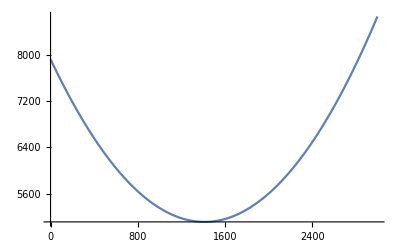

```mathematica
forFitG=dataG⟦2;;,{2,3}⟧;
fitG=LinearModelFit[forFitG,{1,x,x^2},x]
fitG@"ParameterTable"
Plot[fitG["Function"]@x, {x, 0, 3000}]
```

```mathematica
{{"", "Estimate", "Standard Error"}, {1, 7931.342046225647, 249.70710941452646}, {x, -3.9955454907650885, 0.22123570012579102}, {x^2, 0.001414286956914601, 0.00004891268286637867}}
```

{{,Estimate,Standard Error},{1,7931.34,249.707},{x,-3.99555,0.221236},{x^2,0.00141429,0.0000489127}}

```mathematica
TeXForm[{{"","Estimate","Standard Error"},{1,7931.342046225647,249.70710941452646},{x,-3.9955454907650885,0.22123570012579102},{x^2,0.001414286956914601,0.00004891268286637867}}]
```

\left(
\begin{array}{ccc}
 \text{} & \text{Estimate} & \text{Standard Error} \\
 1 & 7931.34 & 249.707 \\
 x & -3.99555 & 0.221236 \\
 x^2 & 0.00141429 & 0.0000489127 \\
\end{array}
\right)

```mathematica
f_x=fitG["Function"]
```

7931.34-3.99555 #1+0.00141429 #1^2&

```mathematica
(7931.342046225647-3.9955454907650885 #1+0.001414286956914601 #1^2&)[1872]
```

5407.89

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.5}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,100}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

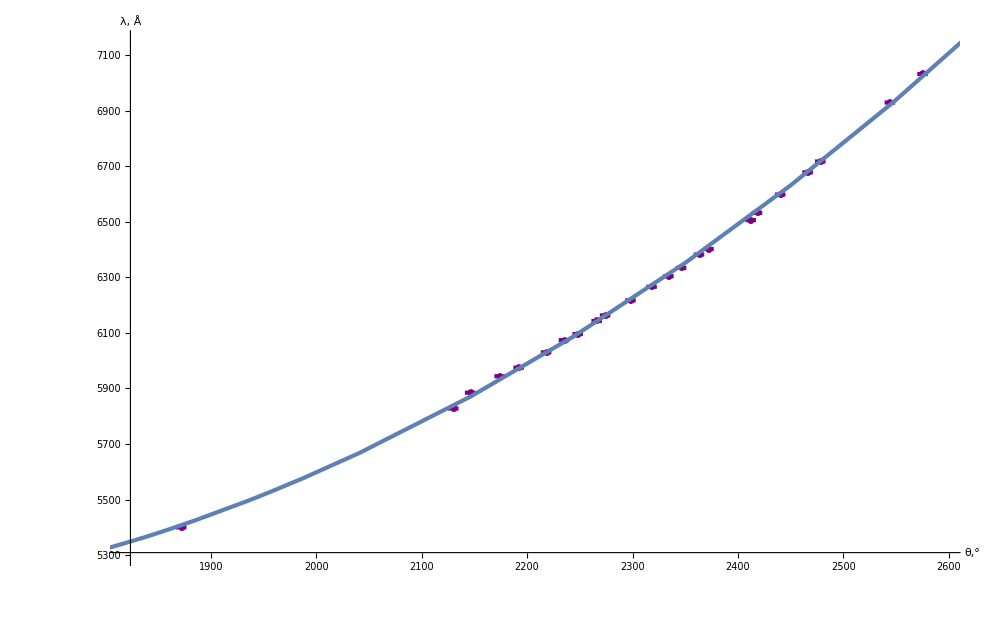

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataG⟦2;;,{2,3,4,1}⟧,
GridLines->{grids@25,grids@50},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"θ,°","λ, Å"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
(*vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),*)
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
Ticks->{Automatic,myTicY},
PlotRange->{{1820,2595},{5300,7150}}], 
Plot[fitG["Function"]@x,{x,0,5000}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeXg=MapAt[dropLastDot@*ToString,dataG,{{2;;,All}}];
forTeXg//TeXForm
```

\left(
\begin{array}{ccc}
 \unicode{2116}\unicode{043b}\unicode{0438}\unicode{043d}\unicode{0438}\unicode{0438} &
   \unicode{0433}\unicode{0440}\unicode{0430}\unicode{0434}\unicode{0443}\unicode{0441}\unicode{044b} & \text{$\backslash \backslash $lambda} \\
 23 & 1872 & 5400 \\
 22 & 2130 & 5828 \\
 21 & 2146 & 5885 \\
 20 & 2174 & 5944 \\
 19 & 2192 & 5975 \\
 18 & 2218 & 6030 \\
 17 & 2235 & 6074 \\
 16 & 2248 & 6096 \\
 15 & 2266 & 6143 \\
 14 & 2274 & 6163 \\
 13 & 2298 & 6217 \\
 12 & 2318 & 6266 \\
 11 & 2334 & 6304 \\
 10 & 2346 & 6334 \\
 9 & 2363 & 6382 \\
 8 & 2372 & 6402 \\
 7 & 2412 & 6506 \\
 6 & 2418 & 6532 \\
 5 & 2440 & 6598 \\
 4 & 2466 & 6678 \\
 3 & 2478 & 6717 \\
 2 & 2544 & 6929 \\
 1 & 2575 & 7032 \\
\end{array}
\right)

## Построение одного графика

### Импорт табличных данных

```mathematica
dataIbig=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/11/tables/Ibig.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataIbig//TableForm
```

№ | V | I |  |  | 
1. | 6.797 | 0.586 | 0.2 | 0.766 | 0.048
2. | 6.223 | 0.582 | 0.2 | 0.763 | 0.048
3. | 5.782 | 0.577 | 0.2 | 0.76 | 0.048
4. | 5.235 | 0.571 | 0.2 | 0.756 | 0.048
5. | 4.701 | 0.563 | 0.2 | 0.75 | 0.048
6. | 4.2 | 0.556 | 0.2 | 0.746 | 0.047
7. | 3.64 | 0.545 | 0.2 | 0.738 | 0.047
8. | 3.06 | 0.531 | 0.2 | 0.729 | 0.047
9. | 2.565 | 0.515 | 0.2 | 0.718 | 0.047
10. | 2.1 | 0.489 | 0.2 | 0.699 | 0.047
11. | 1.43 | 0.44 | 0.2 | 0.663 | 0.047
12. | 0.9 | 0.34 | 0.2 | 0.583 | 0.046
13. | 0.41 | 0.173 | 0.2 | 0.416 | 0.044
14. | 0.02 | 0.069 | 0.2 | 0.263 | 0.043
15. | -0.02 | 0.057 | 0.2 | 0.239 | 0.042
16. | -0.18 | 0.034 | 0.2 | 0.184 | 0.042
17. | -0.3 | 0.015 | 0.2 | 0.122 | 0.041
18. | -1.125 | -0.005 | 0.2 | -0.071 | 0.041
19. | -1.75 | -0.005 | 0.2 | -0.071 | 0.041
20. | -3.04 | -0.005 | 0.2 | -0.071 | 0.041

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
dataIbigfit=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/11/tables/fitbig.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataIbigfit//TableForm
```

№ |  |  |  |  | 
12. | 0.9 | 0.34 | 0.2 | 0.583095 | 0.0408167
13. | 0.41 | 0.173 | 0.2 | 0.415933 | 0.0291153
14. | 0.02 | 0.069 | 0.2 | 0.262679 | 0.0183875
15. | -0.02 | 0.057 | 0.2 | 0.238747 | 0.0167123
16. | -0.18 | 0.034 | 0.2 | 0.184391 | 0.0129074
17. | -0.3 | 0.015 | 0.2 | 0.122474 | 0.00857321

FittedModel[0.248515+0.381001 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.248515 | 0.0043133 | 57.6158 | 5.4339×10^-7
x | 0.381001 | 0.0100678 | 37.8437 | 2.91177×10^-6

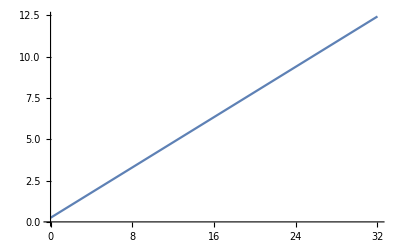

```mathematica
forFitBig=dataIbigfit⟦2;;,{2,5}⟧;
fitBig=LinearModelFit[forFitBig,{1,x},x]
fitBig@"ParameterTable"
Plot[fitBig["Function"]@x, {x, 0, 32}]
```

```mathematica
0.24202290663098904/0.38068655405688974
```

0.635754

```mathematica
Sqrt[(0.0116165/0.2620229066309890)^2+(0.019977101190738266/0.33068655405688974)^2]
```

0.0749332

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,1}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,100}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

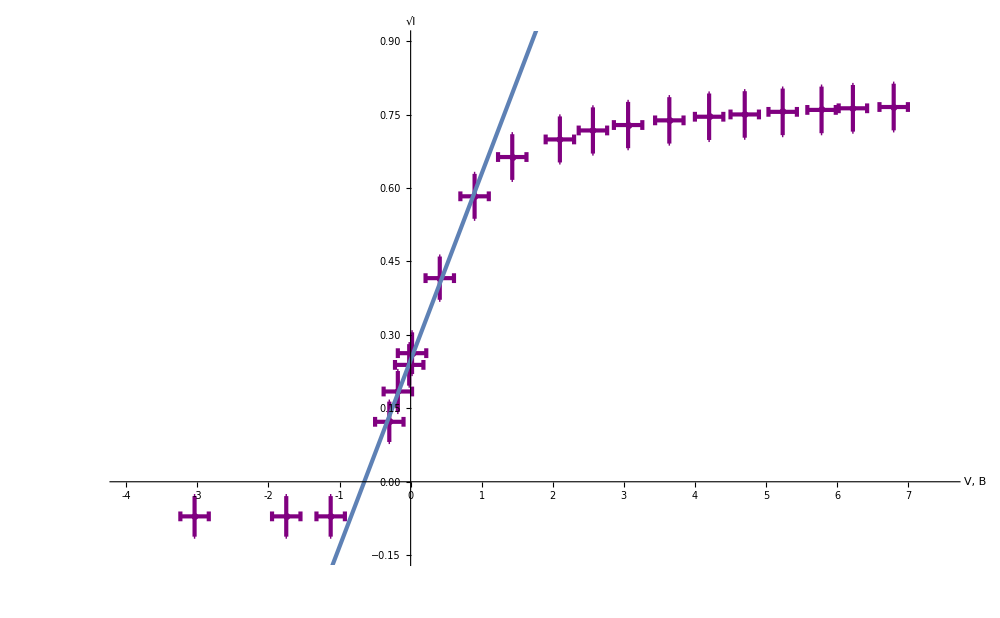

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataIbig⟦2;;,{2,5,4,6}⟧,
GridLines->{grids@0.25,grids@0.1},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"V, В","√I"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
Ticks->{myTicX,Automatic},
PlotRange->{{-4,7.5},{-0.15,0.9}}], 
Plot[fitBig["Function"]@x,{x,-10,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeXB=MapAt[dropLastDot@*ToString,dataIbig⟦2;;,{1,2,3,5}⟧];
forTeXB//TeXForm
```

\text{MapAt}\left[\text{dropLastDot}\text{@*}\text{ToString},\left(
\begin{array}{cccc}
 1. & 6.797 & 0.586 & 0.766 \\
 2. & 6.223 & 0.582 & 0.763 \\
 3. & 5.782 & 0.577 & 0.76 \\
 4. & 5.235 & 0.571 & 0.756 \\
 5. & 4.701 & 0.563 & 0.75 \\
 6. & 4.2 & 0.556 & 0.746 \\
 7. & 3.64 & 0.545 & 0.738 \\
 8. & 3.06 & 0.531 & 0.729 \\
 9. & 2.565 & 0.515 & 0.718 \\
 10. & 2.1 & 0.489 & 0.699 \\
 11. & 1.43 & 0.44 & 0.663 \\
 12. & 0.9 & 0.34 & 0.583 \\
 13. & 0.41 & 0.173 & 0.416 \\
 14. & 0.02 & 0.069 & 0.263 \\
 15. & -0.02 & 0.057 & 0.239 \\
 16. & -0.18 & 0.034 & 0.184 \\
 17. & -0.3 & 0.015 & 0.122 \\
 18. & -1.125 & -0.005 & -0.071 \\
 19. & -1.75 & -0.005 & -0.071 \\
 20. & -3.04 & -0.005 & -0.071 \\
\end{array}
\right)\right]

## Построение одного графика

### Импорт табличных данных

```mathematica
dataI2235=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/11/tables/I2235.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataI2235//TableForm
```

№ | V | I |  |  | 
1. | 0.939 | 0.328 | 0.15 | 0.573 | 0.041
2. | 0.645 | 0.248 | 0.15 | 0.498 | 0.04
3. | 0.24 | 0.119 | 0.15 | 0.345 | 0.038
4. | 0.399 | 0.178 | 0.15 | 0.422 | 0.039
5. | 0.695 | 0.282 | 0.15 | 0.531 | 0.04
6. | 0.077 | 0.081 | 0.15 | 0.285 | 0.038
7. | 0.02 | 0.069 | 0.15 | 0.263 | 0.038
8. | -0.835 | 0.003 | 0.15 | 0.055 | 0.036

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFit2235=dataI2235⟦2;;,{2,5}⟧;
```

FittedModel[0.263619+0.355079 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.263619 | 0.0108196 | 24.3649 | 2.17106×10^-6
x | 0.355079 | 0.0202219 | 17.5591 | 0.0000109854

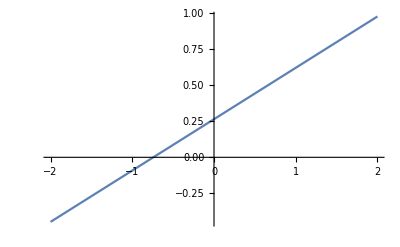

```mathematica
fit2235=LinearModelFit[forFit2235,{1,x},x]
fit2235@"ParameterTable"
Plot[fit2235["Function"]@x, {x, -2, 2}]
```

```mathematica
0.2636186837509491/0.35507876969892016
```

0.742423

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX2235[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.25}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,100}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

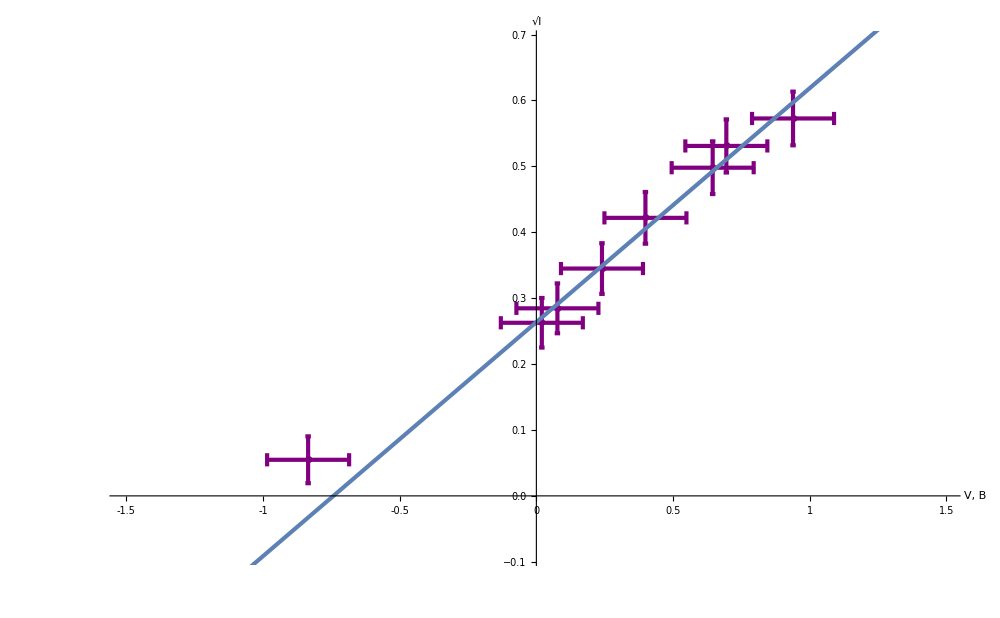

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataI2235⟦2;;,{2,5,4,6}⟧,
GridLines->{grids@0.1,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"V, В","√I"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
Ticks->{myTicX2235,Automatic},
PlotRange->{{-1.5,1.49},{-0.09,0.69}}], 
Plot[fit2235["Function"]@x,{x,-35,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX2235=MapAt[dropLastDot@*ToString,dataI2235⟦2;;,{1,2,3,5}⟧];
forTeX2235//TeXForm
```

\text{MapAt}\left[\text{dropLastDot}\text{@*}\text{ToString},\left(
\begin{array}{cccc}
 1. & 0.939 & 0.328 & 0.573 \\
 2. & 0.645 & 0.248 & 0.498 \\
 3. & 0.24 & 0.119 & 0.345 \\
 4. & 0.399 & 0.178 & 0.422 \\
 5. & 0.695 & 0.282 & 0.531 \\
 6. & 0.077 & 0.081 & 0.285 \\
 7. & 0.02 & 0.069 & 0.263 \\
 8. & -0.835 & 0.003 & 0.055 \\
\end{array}
\right)\right]

## Построение одного графика

### Импорт табличных данных

```mathematica
dataI2412=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/11/tables/2412.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataI2412//TableForm
```

№ | V | I |  |  | 
1. | 0.899 | 0.362 | 0.15 | 0.602 | 0.041
2. | 0.654 | 0.282 | 0.15 | 0.531 | 0.04
3. | 0.415 | 0.189 | 0.15 | 0.435 | 0.039
4. | 0.24 | 0.13 | 0.15 | 0.361 | 0.039
5. | 0.01 | 0.055 | 0.15 | 0.235 | 0.037
6. | -0.372 | 0.002 | 0.15 | 0.045 | 0.035

### Фитирование табличных данных линейной функцией

```mathematica
forFit2412=dataI2412⟦2;;,{2,5}⟧;
```

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[0.230778+0.445597 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.230778 | 0.0120653 | 19.1274 | 0.0000440208
x | 0.445597 | 0.0233336 | 19.0968 | 0.000044301

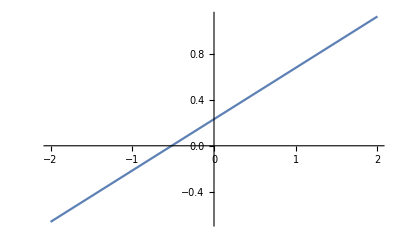

```mathematica
fit2412=LinearModelFit[forFit2412,{1,x},x]
fit2412@"ParameterTable"
Plot[fit2412["Function"]@x, {x, -2, 2}]
```

```mathematica
0.23077803624752524/0.4455966631320809
```

0.517908

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX2235[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.25}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,100}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

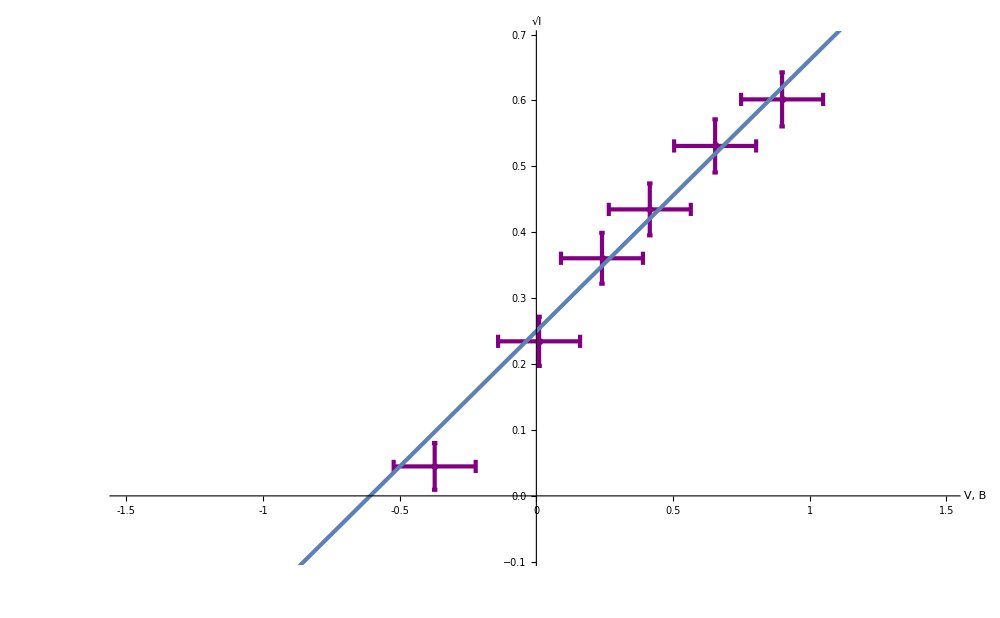

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataI2412⟦2;;,{2,5,4,6}⟧,
GridLines->{grids@0.1,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"V, В","√I"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
Ticks->{myTicX2235,Automatic},
PlotRange->{{-1.5,1.49},{-0.09,0.69}}], 
Plot[fit2412["Function"]@x,{x,-35,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX2412=MapAt[dropLastDot@*ToString,dataI2412⟦2;;,{1,2,3,5}⟧];
forTeX2412//TeXForm
```

\text{MapAt}\left[\text{dropLastDot}\text{@*}\text{ToString},\left(
\begin{array}{cccc}
 1. & 0.899 & 0.362 & 0.602 \\
 2. & 0.654 & 0.282 & 0.531 \\
 3. & 0.415 & 0.189 & 0.435 \\
 4. & 0.24 & 0.13 & 0.361 \\
 5. & 0.01 & 0.055 & 0.235 \\
 6. & -0.372 & 0.002 & 0.045 \\
\end{array}
\right)\right]

## Построение одного графика

### Импорт табличных данных

```mathematica
dataI2318=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/11/tables/2318.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataI2318//TableForm
```

№ | V | I |  |  | 
1. | 0.77 | 0.29 | 0.15 | 0.539 | 0.04
2. | 0.55 | 0.23 | 0.15 | 0.48 | 0.04
3. | 0.358 | 0.16 | 0.15 | 0.4 | 0.039
4. | 0.083 | 0.077 | 0.15 | 0.277 | 0.038
5. | -0.022 | 0.052 | 0.15 | 0.228 | 0.037
6. | -0.147 | 0.027 | 0.15 | 0.164 | 0.037
7. | -0.45 | 0.003 | 0.15 | 0.055 | 0.036

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

FittedModel[0.238741+0.412892 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.238741 | 0.00553726 | 43.1154 | 1.2666×10^-7
x | 0.412892 | 0.0130772 | 31.5735 | 5.98461×10^-7

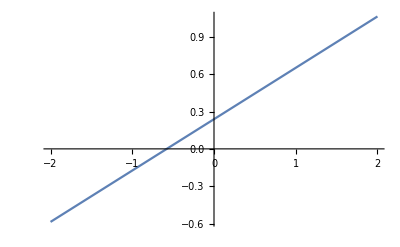

```mathematica
forFit2318=dataI2318⟦2;;,{2,5}⟧;
fit2318=LinearModelFit[forFit2318,{1,x},x]
fit2318@"ParameterTable"
Plot[fit2318["Function"]@x, {x, -2, 2}]
```

```mathematica
0.23874140175044453/0.41289200291045247
```

0.578218

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX2235[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.25}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,100}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

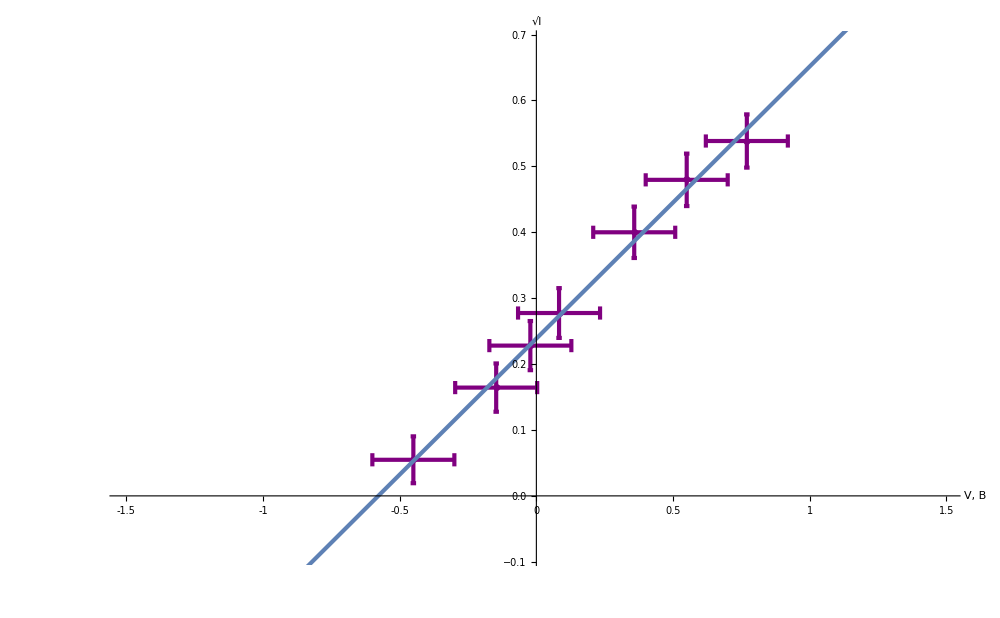

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataI2318⟦2;;,{2,5,4,6}⟧,
GridLines->{grids@0.1,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"V, В","√I"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
Ticks->{myTicX2235,Automatic},
PlotRange->{{-1.5,1.49},{-0.09,0.69}}], 
Plot[fit2318["Function"]@x,{x,-35,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX2318=MapAt[dropLastDot@*ToString,dataI2318⟦2;;,{1,2,3,5}⟧];
forTeX2318//TeXForm
```

\text{MapAt}\left[\text{dropLastDot}\text{@*}\text{ToString},\left(
\begin{array}{cccc}
 1. & 0.77 & 0.29 & 0.539 \\
 2. & 0.55 & 0.23 & 0.48 \\
 3. & 0.358 & 0.16 & 0.4 \\
 4. & 0.083 & 0.077 & 0.277 \\
 5. & -0.022 & 0.052 & 0.228 \\
 6. & -0.147 & 0.027 & 0.164 \\
 7. & -0.45 & 0.003 & 0.055 \\
\end{array}
\right)\right]

## Построение одного графика

### Импорт табличных данных

```mathematica
dataI1872=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/11/tables/1872.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataI1872//TableForm
```

№ | V | I |  |  | 
1. | 1.417 | 0.322 | 0.15 | 0.567 | 0.041
2. | 1.07 | 0.253 | 0.15 | 0.503 | 0.04
3. | 0.76 | 0.182 | 0.15 | 0.427 | 0.039
4. | 0.41 | 0.117 | 0.15 | 0.342 | 0.038
5. | 0.12 | 0.075 | 0.15 | 0.274 | 0.038
6. | 0. | 0.04 | 0.15 | 0.2 | 0.037
7. | -0.128 | 0.025 | 0.15 | 0.158 | 0.037
8. | -0.754 | -0.016 | 0.15 | -0.126 | 0.036

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFit1872=dataI1872⟦2;;,{2,5}⟧;
```

FittedModel[0.216402+0.262064 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.216402 | 0.0116755 | 18.5347 | 8.41251×10^-6
x | 0.262064 | 0.0155836 | 16.8166 | 0.0000135923

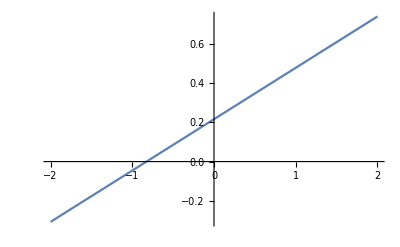

```mathematica
fit1872=LinearModelFit[forFit1872,{1,x},x]
fit1872@"ParameterTable"
Plot[fit1872["Function"]@x, {x, -2, 2}]
```

```mathematica
0.21640173284223757/0.26206405357959095
```

0.825759

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX2235[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.25}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,100}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

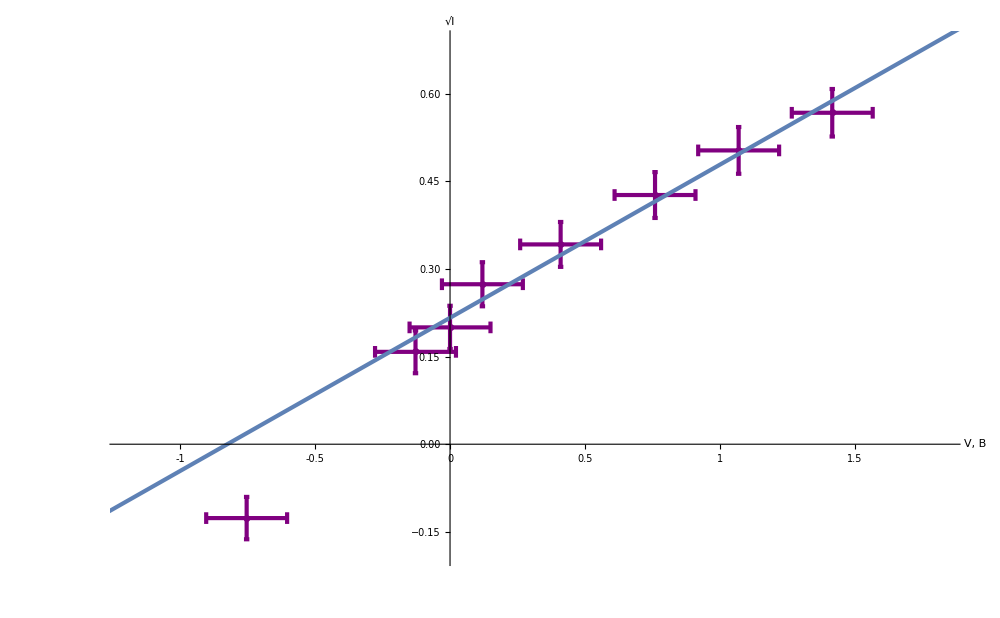

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataI1872⟦2;;,{2,5,4,6}⟧,
GridLines->{grids@0.1,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"V, В","√I"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)
}],
Ticks->{myTicX2235,Automatic},
PlotRange->{{-1.2,1.83},{-0.19,0.69}}], 
Plot[fit1872["Function"]@x,{x,-35,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeX1872=MapAt[dropLastDot@*ToString,dataI1872⟦2;;,{1,2,3,5}⟧];
forTeX1872//TeXForm
```

\text{MapAt}\left[\text{dropLastDot}\text{@*}\text{ToString},\left(
\begin{array}{cccc}
 1. & 1.417 & 0.322 & 0.567 \\
 2. & 1.07 & 0.253 & 0.503 \\
 3. & 0.76 & 0.182 & 0.427 \\
 4. & 0.41 & 0.117 & 0.342 \\
 5. & 0.12 & 0.075 & 0.274 \\
 6. & 0. & 0.04 & 0.2 \\
 7. & -0.128 & 0.025 & 0.158 \\
 8. & -0.754 & -0.016 & -0.126 \\
\end{array}
\right)\right]

## Построение одного графика

### Импорт табличных данных

```mathematica
dataV0=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/5sem/11/tables/V0.xlsx"]⟦1,All,1;;⟧,Except[{"Таблица 1"|"",""..}]];
dataV0//TableForm
```

№ | deg | \lambda | \omega | A | B | V0 | 
1. | 2174. | 5944. | 3.16958 | 0.381001 | 0.248515 | 0.792 | 0.059
2. | 2235. | 6074. | 3.10175 | 0.355079 | 0.263619 | 0.742 | 0.056
3. | 2412. | 6506. | 2.89579 | 0.445597 | 0.230778 | 0.518 | 0.039
4. | 2318. | 6266. | 3.0067 | 0.412892 | 0.238741 | 0.578 | 0.043
5. | 1872. | 5400. | 3.48889 | 0.262064 | 0.216402 | 0.826 | 0.062

### Фитирование табличных данных линейной функцией

В первый столбец “data” указывается величина по оси x, во второй – по y.

```mathematica
forFitV=dataV0⟦2;;,{5,4}⟧;
fitV=LinearModelFit[forFitV,{1,x},x]
fitV@"ParameterTable"
Plot[fitV["Function"]@x, {x, -2, 2}]
```

FittedModel[-0.949185+0.523702 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.949185 | 0.550717 | -1.72354 | 0.183261
x | 0.523702 | 0.175446 | 2.98498 | 0.0583643

```mathematica
{{"", "Estimate", "Standard Error"}, {1, -0.9491845318387957, 0.5507171072421373}, {x, 0.523701941038647, 0.1754458528429999}}
```

{{,Estimate,Standard Error},{1,-0.949185,0.550717},{x,0.523702,0.175446}}

```mathematica
TeXForm[{{"","Estimate","Standard Error"},{1,-0.9491845318387957,0.5507171072421373},{x,0.523701941038647,0.1754458528429999}}]
```

\left(
\begin{array}{ccc}
 \text{} & \text{Estimate} & \text{Standard Error} \\
 1 & -0.949185 & 0.550717 \\
 x & 0.523702 & 0.175446 \\
\end{array}
\right)

### Создание своих Ticks для графика

Последняя ячейка – значение тика по соответствующей оси

```mathematica
myTicX2235[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,0.25}]
```

```mathematica
myTicY[min_,max_]:=Table[{i,dropLastDot@ToString@i},{i,Floor@min,Ceiling@max,100}]
```

### Построение графика линейной функции + табличные данные с крестами погрешностей

В переменную “data” указываются табличные данные в формате “{столбец данных оси х, столбец данных оси y, погрешность данных оси х, погрешность данных оси y}.
В случае, если нужна погрешность только по одной оси, в “data” ненужной оси записывается произвольный столбец, а в коде ниже соответствующие “Cross” закомменчиваются.
В переменную “fit” указывается отфитированная выше функция, соответствующая этим табличным данным.

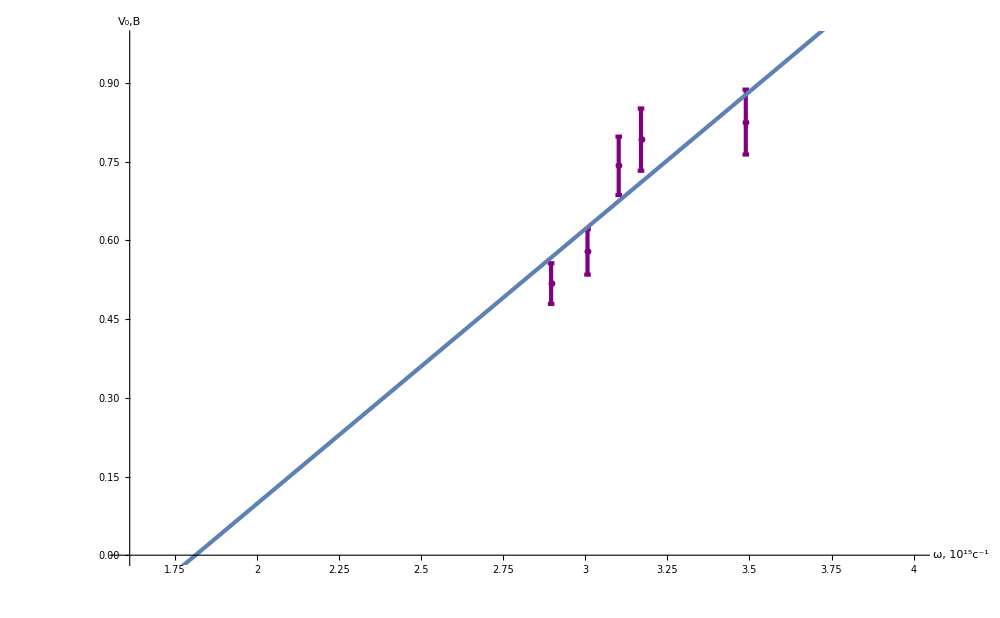

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@dataV0⟦2;;,{5,4,6,6}⟧,
GridLines->{grids@0.1,grids@0.05},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"ω, 10^15c^-1","V_0,В"},
AxesStyle->Directive[Large,Black],PlotMarkers->Automatic,PlotStyle-> Purple,ImageSize->1000,
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,
vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords)(*,
horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)*)
}],
Ticks->{myTicX2235,Automatic},
PlotRange->{{1.6,4},{0,0.98}}], 
Plot[fitV["Function"]@x,{x,-35,35}, PlotStyle->Thickness@0.003]]
```

#### Экспорт табличных данных в LATEX формат

```mathematica
forTeXV0=MapAt[dropLastDot@*ToString,dataV0,{{2;;,All}}];
forTeXV0//TeXForm
```

\left(
\begin{array}{cccccccc}
 \unicode{2116} & \text{deg} & \text{$\backslash \backslash $lambda} &
   \text{$\backslash \backslash $omega} & \text{A} & \text{B} & \text{V0} &
   \text{} \\
 1 & 2174 & 5944 & 3.16958 & 0.381001 & 0.248515 & 0.792 & 0.059 \\
 2 & 2235 & 6074 & 3.10175 & 0.355079 & 0.263619 & 0.742 & 0.056 \\
 3 & 2412 & 6506 & 2.89579 & 0.445597 & 0.230778 & 0.518 & 0.039 \\
 4 & 2318 & 6266 & 3.0067 & 0.412892 & 0.238741 & 0.578 & 0.043 \\
 5 & 1872 & 5400 & 3.48889 & 0.262064 & 0.216402 & 0.826 & 0.062 \\
\end{array}
\right)

```mathematica
0.523701941038647*10^-15*1.6021766208*10^-19
```

8.39063×10^-35

```mathematica
0.1754458528429999/0.523701941038647
```

0.335011

```mathematica
0.3350108890088164*8.390630061997003*^-35
```

2.81095×10^-35

```mathematica
0.9491845318387957/0.523701941038647
```

```mathematica
(2*Pi*3*10^8)/(1.812451811723856*10^15)
```

1.04×10^-6

```mathematica
Sqrt[0.3350108890088164^2+(0.5507171072421373/0.9491845318387957)^2]
```

```mathematica
0.6699736050362773
```